```mathematica
RandomFunction[BinomialProcess[1/3],{0,50}]
```

TemporalData[…]

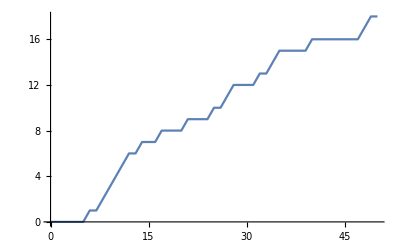

```mathematica
ListLinePlot[%1]
```

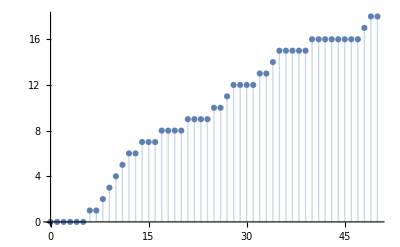

```mathematica
ListPlot[Out[1],Filling->Axis]
```

```mathematica
RandomFunction[ARProcess[{0.7},1],{0,50}]
```

TemporalData[…]

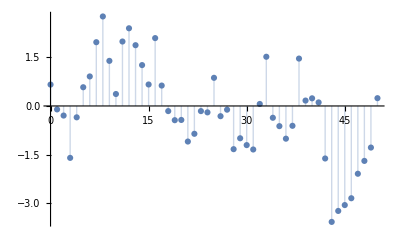

```mathematica
ListPlot[Out[5],Filling->Axis,AxesOrigin->{0,0}]
```

```mathematica
RandomFunction[WienerProcess[],{0,10,0.1}]
```

TemporalData[…]

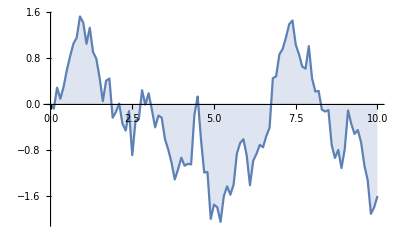

```mathematica
ListLinePlot[Out[7],Filling->Axis,AxesOrigin->{0,0}]
```

```mathematica
RandomFunction[WienerProcess[],{0,10,0.1},10]
```

TemporalData[…]

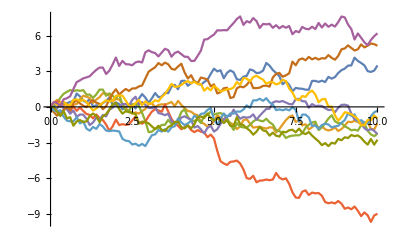

```mathematica
ListLinePlot[%]
```

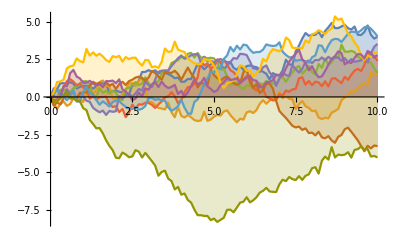

```mathematica
ListLinePlot[RandomFunction[WienerProcess[],{0,10,0.1},10],Filling->Axis]
```

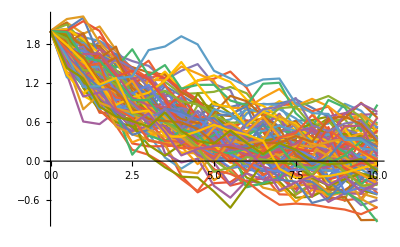

```mathematica
ListLinePlot[
RandomFunction[OrnsteinUhlenbeckProcess[0,.3,.3,2],{0,10,.5},10^2]
,Joined->True]
```

```mathematica
amzn=FinancialData["NASDAQ:AMZN","Close",All]
```

TimeSeries[…]

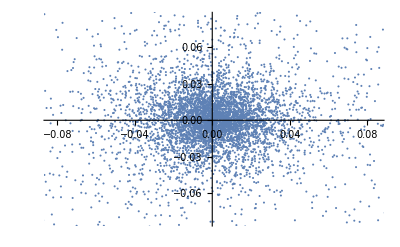

```mathematica
ListPlot@
Partition[
Map[#-1&,Ratios@amzn["Values"]]
,2,1]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

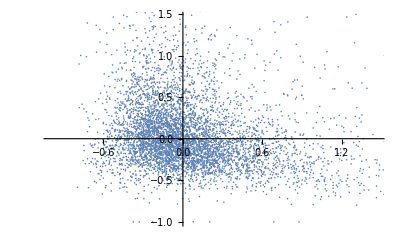

```mathematica
ListPlot@
Partition[
Map[#-1&,Ratios[FinancialData["NASDAQ:AMZN","Volume",All]["Values"]]]
,2,1]
```

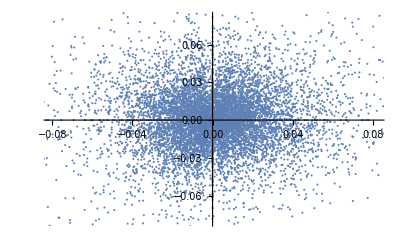

```mathematica
ListPlot@
Partition[
Map[#-1&,Ratios[FinancialData["NASDAQ:AAPL","Close",All]["Values"]]]
,2,1]
```

```mathematica
Histogram3D@
Partition[
Map[#-1&,Ratios[FinancialData["NASDAQ:AAPL","Close",All]["Values"]]]
,2,1]
```

-Graphics3D-

```mathematica
Histogram3D@
Partition[
Map[#-1&,Ratios[FinancialData["NASDAQ:AMZN","Volume",All]["Values"]]]
,2,1]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

-Graphics3D-

```mathematica
ListPlot@
Partition[
Map[#-1&,Differences@
amzn["Values"]]
,2,1]
```

-Graphics-

```mathematica
ListPlot@
Partition[
Map[#-1&,Differences[FinancialData["NASDAQ:AAPL","Close",All]["Values"]]]
,2,1]
```

-Graphics-

```mathematica
Partition[
Map[#-1&,
Differences[
FinancialData["NASDAQ:AAPL","Close",All]["Values"]]]
,2,1]
```

{{-1+-0.03 $,-1+-0.04 $},{-1+-0.04 $,-1+0.01 $},{-1+0.01 $,-1+0.01 $},{-1+0.01 $,-1+0.03 $},{-1+0.03 $,-1+0.02 $},{-1+0.02 $,-1+0.02 $},{-1+0.02 $,-1+0.03 $},{-1+0.03 $,-1+0.05 $},{-1+0.05 $,-1+0.01 $},{-1+0.01 $,-1+-0.02 $},{-1+-0.02 $,-1+-0.02 $},9837,{-1+0.27 $,-1+5.64 $},{-1+5.64 $,-1+-0.11 $},{-1+-0.11 $,-1+1.72 $},{-1+1.72 $,-1+2.13 $},{-1+2.13 $,-1+6.70 $},{-1+6.70 $,-1+-2.92 $},{-1+-2.92 $,-1+2.37 $},{-1+2.37 $,-1+-1.41 $},{-1+-1.41 $,-1+4.80 $},{-1+4.80 $,-1+6.44 $},{-1+6.44 $,-1+0.70 $}}
 |  |  |  |

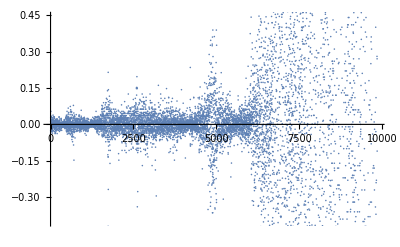

```mathematica
Partition[
ListPlot@
Differences[
FinancialData["NASDAQ:AAPL","Close",All]["Values"]]
,2,1]
```

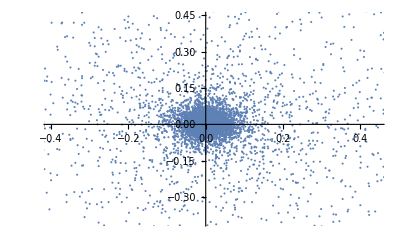

```mathematica
ListPlot@
Partition[
Differences[
FinancialData["NASDAQ:AAPL","Close",All]["Values"]]
,2,1]
```

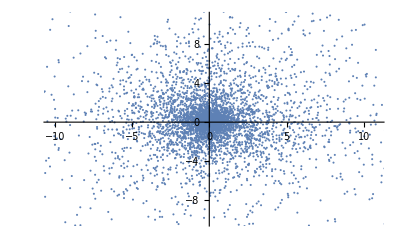

```mathematica
ListPlot@
Partition[
Differences[
FinancialData["NASDAQ:AMZN","Close",All]["Values"]]
,2,1]
```

```mathematica
Histogram3D@
Partition[
Differences[
FinancialData["NASDAQ:AMZN","Close",All]["Values"]]
,2,1]
```

-Graphics3D-

```mathematica
ListPlot[
Partition[
Differences[
FinancialData["NASDAQ:AMZN","Close",All]["Values"]]
,2,1]
,PlotTheme->"Marketing",ColorFunction->"DarkRainbow"
]
```

-Graphics-

```mathematica
ListPlot[
Partition[
Differences[
FinancialData["NASDAQ:AMZN","Close",All]["Values"]]
,2,1]
,PlotTheme->"Marketing"
]
```

-Graphics-